```mathematica
SetDirectory[NotebookDirectory[]];
datav=Import["data_for_voltage.csv"];
datac=Import["data_for_columns.csv"];
datar=Import["data_for_rows.csv"];
dataRC=Import["data_for_columns_and_rows.csv"];
dataVC=Import["data_for_voltage_and_columns.csv"];
dataRV=Import["data_for_rows_and_voltages.csv"];
datamore=Import["data_for_more.csv"];
datamore3=Import["data_for_more3.csv"];
data4=Import["data_for_more4.csv"];
datagears=Import["data_for_gears.csv"];
dataRV2=Import["data_for_v2.csv"];
pillarsdistribution=Import["fail_timep.csv"];
gearsdistribution=Import["fail_timeg.csv"];
```

```mathematica
(*for pillars*)
```

```mathematica
(*plot for v and c*)
```

```mathematica
Do[average={};variance={};mintime={};maxtime={};Do[average=Append[average,{dataVC[[2+i*25+j,1]],dataVC[[2+i*25+j,3]],dataVC[[2+i*25+j,4]]}];
,{j,0,24}];
name=Switch[i,0,"failure time of pillars for 20 rows ",1,"failure time of pillars for 100 rows ",2,
"failure time of pillars 180 rows "];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"columns","voltage","steps"},PlotLabel->name];
Print[pa];
,{i,0,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*r and v*)
```

```mathematica
Do[average={};variance={};mintime={};maxtime={};Do[average=Append[average,{dataRV[[2+i*25+j,2]],dataRV[[2+i*25+j,3]],dataRV[[2+i*25+j,4]]}];
,{j,0,24}];
name=Switch[i,0,"failure time of pillars for 100 columns ",1,"failure time of pillars for 550 columns ",2,
"failure time of pillars 1000 columns "];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"rows","voltage","steps"},PlotLabel->name];
Print[pa];
,{i,0,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
average={};
Do[average=Append[average,{dataRV2[[2+j,2]],dataRV2[[2+j,3]],dataRV2[[2+j,4]]}];
,{j,0,41}];
name="failure time of pillars for 200 columns ";
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"rows","voltage","steps"},PlotLabel->name]
average={};
Do[average=Append[average,{dataRV2[[2+j,2]],dataRV2[[2+j,3]],dataRV2[[2+j,4]]}];
,{j,0,11}];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"rows","voltage","steps"},PlotLabel->name]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*c and r*)
```

```mathematica
Do[average={};variance={};mintime={};maxtime={};Do[average=Append[average,{datamore[[2+i*64+j,1]],datamore[[2+i*64+j,2]],datamore[[2+i*64+j,4]]}];
,{j,0,63}];
name=Switch[i,0,"failure time of pillars for voltage=50 ",1,"failure time of pillars for voltage=150 ",2,
"failure time of pillars voltage=250 ",3,"failure time of pillars for voltage=20"];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"columns","rows","steps"},PlotLabel->name];
Print[pa];
,{i,0,3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

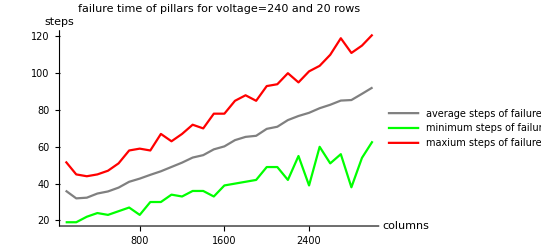

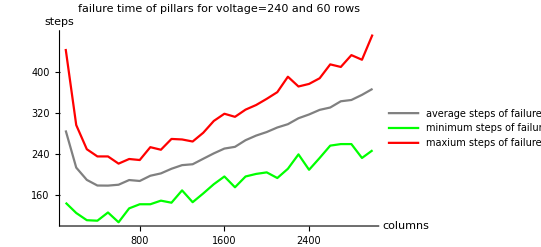

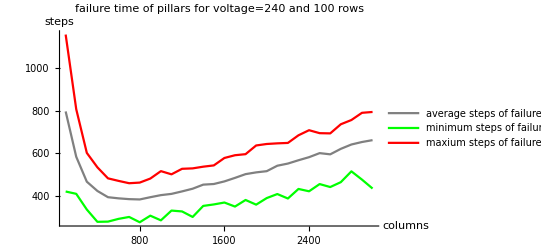

```mathematica
Do[average={};variance={};mintime={};maxtime={};Do[average=Append[average,{(j+1)*100,data4[[2+30*i+j,4]]}];variance=Append[variance,{(j+1)*100,data4[[2+30*i+j,5]]}];mintime=Append[mintime,{(j+1)*100,data4[[2+30*i+j,6]]}];maxtime=Append[maxtime,{(j+1)*100,data4[[2+30*i+j,7]]}];
,{j,0,29}];
pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"}];
pvc=ListLinePlot[variance];
pmin=ListLinePlot[mintime,PlotStyle->Green,PlotLegends->{"minimum steps of failure"}];
pmax=ListLinePlot[maxtime,PlotStyle->Red,PlotLegends->{"maxium steps of failure"}];
name=Switch[i,0,"failure time of pillars for voltage=240 and 20 rows ",1,"failure time of pillars for voltage=240 and 60 rows ",2,
"failure time of pillars for voltage=240 and 100 rows "];
Print[Show[pa,pmin,pmax,AxesOrigin->{0,0},PlotRange->Automatic,AxesLabel->{"columns","steps"},PlotLabel->name]]
,{i,0,2}]
```

```mathematica
Do[average={};variance={};mintime={};maxtime={};Do[average=Append[average,{dataVC[[2+i*25+j,1]],dataVC[[2+i*25+j,3]],dataVC[[2+i*25+j,4]]}];
,{j,0,24}];
name=Switch[i,0,"failure time of pillars for 20 rows ",1,"failure time of pillars for 100 rows ",2,
"failure time of pillars 180 rows "];
pa=ListPlot3D[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"columns","voltage","steps"},PlotLabel->name];
Print[pa];
,{i,0,2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

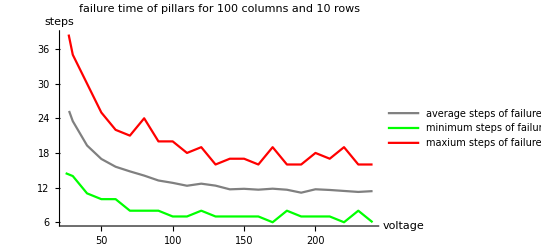

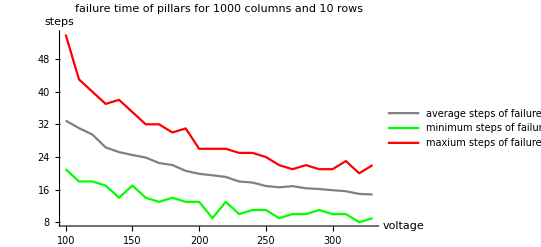

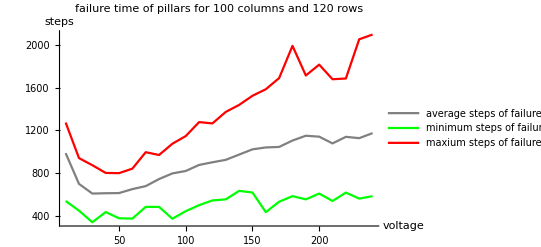

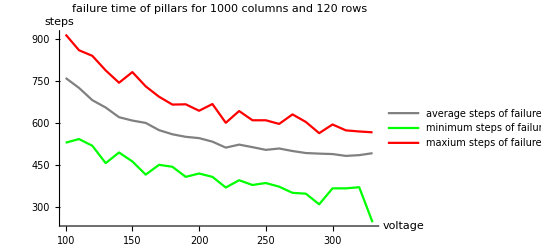

```mathematica
Do[average={};variance={};mintime={};maxtime={};Do[average=Append[average,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,4]]}];variance=Append[variance,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,5]]}];mintime=Append[mintime,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,6]]}];maxtime=Append[maxtime,{(j+1)*10+Switch[i,0,0,1,90,2,0,3,90],datav[[2+24*i+j,7]]}];
,{j,0,23}];
pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of failure"}];
pvv=ListLinePlot[variance];
pmin=ListLinePlot[mintime,PlotStyle->Green,PlotLegends->{"minimum steps of failure"}];
pmax=ListLinePlot[maxtime,PlotStyle->Red,PlotLegends->{"maxium steps of failure"}];
name=Switch[i,0,"failure time of pillars for 100 columns and 10 rows ",1,"failure time of pillars for 1000 columns and 10 rows ",2,
"failure time of pillars for 100 columns and 120 rows ",3,"failure time of pillars for 1000 columns and 120 rows "];
Print[Show[pa,pmin,pmax,AxesOrigin->{0,0},PlotRange->Automatic,AxesLabel->{"voltage","steps"},PlotLabel->name]];
,{i,0,3}]
```

1. when number of rows increases, need more steps to make the overlap between two columns become zero but resistance decrease, can be seen from the plots, failure time always increases, so the former factor always dominate,
2.when number of columns increases, the resistance increases, but there are more columns likely to fail, the plot shows at first the later dominates, then when the resistance becomes so big, the former dominates, the voltage is higher, the turning point is righter,the number of rows is greater, the turning point is lefter.
3. when voltage increases, the possibility to evaporate and condense increase, so at first I guess when increase voltage, the pillar will always fail faster, but the plot shows if the number of columns is not far greater then number of rows, the pillar will fail slower when voltage increase.
ThInk about in the pillar there are n columns have resistance R and one column has resistance r, r>>R, for example, r=20 R,

```mathematica
P1(R_)=1-1/Exp[U*(20*R)^0.5/(N*R+20*R)];
P2(R_)=1-1/Exp[U*(R)^0.5/(N*R+20*R)];
A=Plot3D[P1(1),{U,1,150},{N,1,100},PlotStyle->Red];
B=Plot3D[P2(1),{U,1,150},{N,1,100},PlotStyle->Green];
Print[Show[A,B]]
```

Set::write: Tag Times in (1-ⅇ^(-(4.47214 U)/(20+N))) R_ is Protected.

Set::write: Tag Times in (1-ⅇ^(-(1. U)/(20+N))) R_ is Protected.

TimeConstrained::timc: Number of seconds 1. is not a positive machine-sized number or Infinity.

Plot3D::invisop: {} must be a valid 2D coordinate.

TimeConstrained::timc: Number of seconds 1. is not a positive machine-sized number or Infinity.

Plot3D::invisop: {} must be a valid 2D coordinate.

-Graphics3D-

we can see when N is small (number of columns is small), the higher the voltage, the closer the two possibility, which ,means the possibility of the shortest column be repaired will be greater, so the pillar will fail slower.

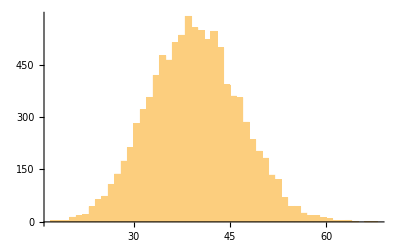

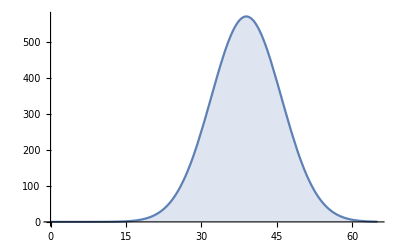

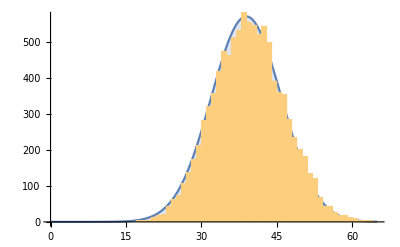

```mathematica
failTimeP=Flatten[pillarsdistribution];
HP=Histogram[failTimeP,100]
averagep=0;
averagepsquare=0;
Do[averagep=averagep+failTimeP[[i]];
averagepsquare=averagepsquare+failTimeP[[i]]^2,{i,1,10000}]
averagep=N[averagep/10000];
averagepsquare=averagepsquare/10000;
variancep=N[averagepsquare-averagep^2];
disp=Plot[10000*PDF[NormalDistribution[averagep,variancep^0.5],x],{x,0,65},Filling->Axis]
Show[disp,HP]
```

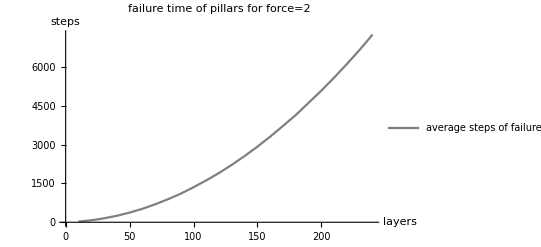

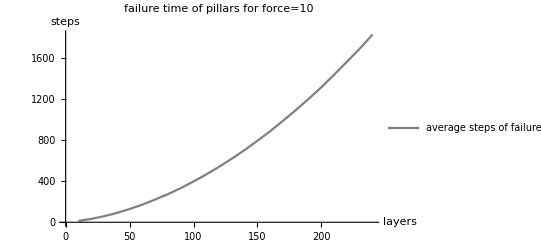

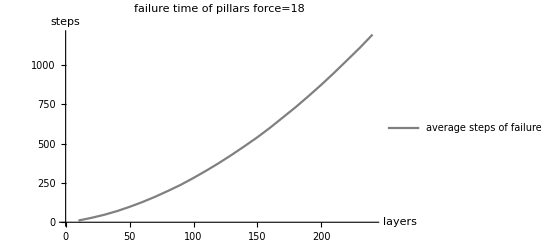

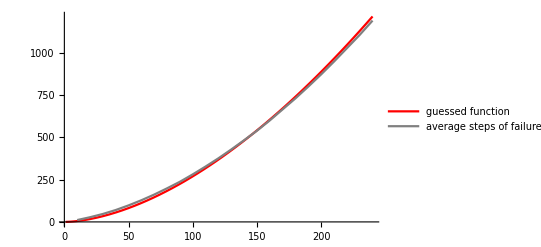

```mathematica
(*like a normaldistribution*)

(*for gears*)
(*number of layers*)
Do[average={};variance={};mintime={};maxtime={};Do[average=Append[average,{datagears[[2+i*24+j,1]],datagears[[2+i*24+j,2]]}];
,{j,0,23}];
name=Switch[i,0,"failure time of pillars for force=2 ",1,"failure time of pillars for force=10 ",2,
"failure time of pillars force=18 "];
pa=ListLinePlot[average,PlotStyle->Gray,AxesOrigin->{0,0},PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"layers","steps"},PlotLabel->name];
Print[pa];
,{i,0,2}]
p=Show[Plot[0.098*  x^1.72,{x,1,240},PlotStyle->Red,AxesOrigin->{0,0},PlotLegends->{"guessed function"}],pa,PlotRange->All]
```

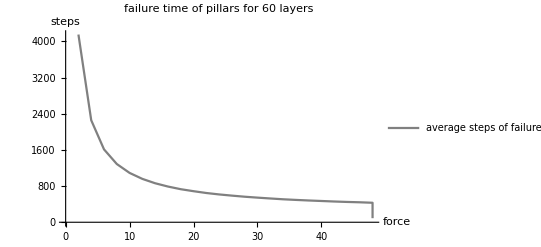

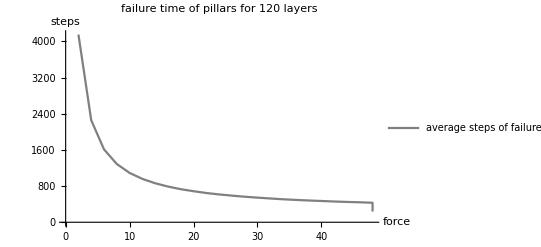

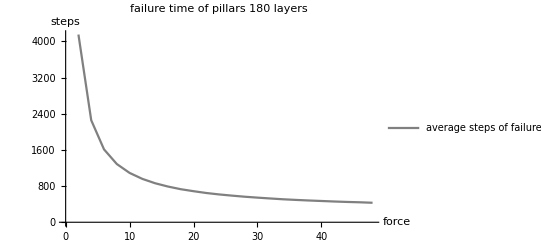

```mathematica
(*force*)
Do[average2={};Do[average2=Append[average,{2*(j+1),datagears[[74+i*24+j,2]]}];
,{j,0,23}];
name=Switch[i,0,"failure time of pillars for 60 layers ",1,"failure time of pillars for 120 layers ",2,
"failure time of pillars 180 layers "];
pa=ListLinePlot[average2,PlotStyle->Gray,AxesOrigin->{0,0},PlotLegends->{"average steps of failure"},PlotRange->All,AxesLabel->{"force","steps"},PlotLabel->name];
Print[pa];
,{i,0,2}]
```

```mathematica
(**)
```

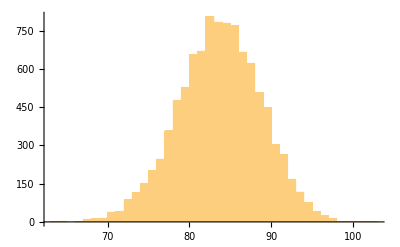

83.1678

25.2646

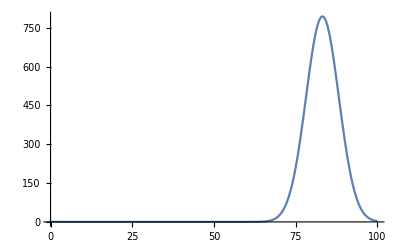

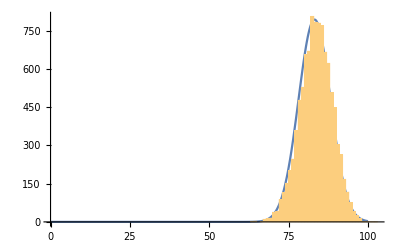

```mathematica
failTimeG=Flatten[gearsdistribution];
HG=Histogram[failTimeG,100]

averageG=0;
averageGsquare=0;
Do[averageG=averageG+failTimeG[[i]];
averageGsquare=averageGsquare+failTimeG[[i]]^2,{i,1,10000}]
averageG=N[averageG/10000]
averageGsquare=averageGsquare/10000;
varianceG=N[averageGsquare-averageG^2]
disG=Plot[10000*PDF[NormalDistribution[averageG,varianceG^0.5],x],{x,0,100},PlotRange->All]
Show[disG,HG]
```